```mathematica
(*first time installation of MaTeX*)
Needs["PacletManager`"]
PacletInstall["~/Downloads/MaTeX-1.7.10.paclet"]
<<MaTeX`
MaTeX["x^2"]
```

-Graphics-

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/blogit" ]
```

/Users/pjoot/project/figures/blogit

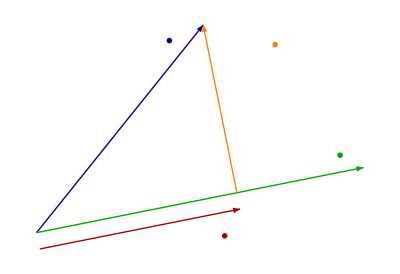

```mathematica
ClearAll[vec2c, c2vec]
vec2c[v_] := Complex[v[[1]], v[[2]]]
c2vec[c_]:={Re[ComplexExpand[c]],Im[ComplexExpand[c]]};


ClearAll[o,e1,e2, x, u, uhat, rotn, xi, ui, rej, projectionFig1]
o = {0,0};
e1 = {1,0};
e2 = {0,1};
rotn[v_, s_ : 1 ] := (s{-e2, e1}.v)//Normalize
x = (e1 + 1.25 e2)/2;

uhat = Normalize[(e1 + 0.2 e2)/3];
u = (x.uhat)uhat;
xi = rotn[x];
ui = rotn[u,-1];

rej = x - u;

projectionFig1 = Graphics[{
Thick, 
Arrowheads -> 0.075, 

Blue // Darker,
Arrow[{o, x}], 
Text[MaTeX["\color{BlueDarker}\\mathbf{x}"], x -0.1 Normalize[x]+ 0.05 xi],

Red // Darker,
Arrow[{0.05 ui, u + 0.05 ui}],
Text[MaTeX["\color{RedDarker}(\\mathbf{x} \cdot \\mathbf{\\hat{u}})\\mathbf{\\hat{u}}"], 0.9 u + 0.12 ui],

Green // Darker,
Arrow[{o, uhat}],
Text[MaTeX["\color{GreenDarker}\\hat{\\mathbf{u}}"], uhat -0.1 u- 0.05 ui],

Orange,
Arrow[{u, x}],
Text[MaTeX["\color{OrangeDarker}\\mathbf{x} - (\\mathbf{x} \cdot \\mathbf{\\hat{u}})\\mathbf{\\hat{u}}"], rej+ u + 0.2 uhat - 0.1 Normalize[rej] ]

}]
```

```mathematica
rotn[e1]
rotn[e2]
```

{0,1}

{-1,0}

```mathematica
peeters`exportForLatex["projectionFig1", projectionFig1]
```

{projectionFig1.eps,projectionFig1pn.png}